```mathematica
mdwout = "/Volumes/homes/Code/cytomod/shila/semiflexible/out/network/";
mdwlcl="/home/simonfreedman/scratch-midway/cytomod/out/network/";
```

```mathematica
ParticleTimeSeries[d_,n_]:=
Module[
{dir=d, name=n},
file=dir<>"/txt_stack/"<>name<>".txt";
particles=Import[file,"Table"];
Print["Finished importing "<>file];
nparticles=Differences[Position[particles,"t",2]][[1,1]]-1;
dt=particles[[2+nparticles,3]];
particlesT=Partition[particles[[2;;]],nparticles, nparticles+1];
{nparticles, dt,particlesT}
];
```

```mathematica
PersistenceLength[d_]:=
Module[
{dir =d},
{np, dt,rt}=ParticleTimeSeries[d,"rods"];
anglesT=ArcTan[rt[[All,All,4]],rt[[All,All,3]]];
ld=Sqrt[rt[[1,1,3]]^+rt[[1,1,4]]^2];
corrs=Table[{(j-i)*ld,Cos[anglesT[[t,j]]-anglesT[[t,i]]]},{t,Length[rt]/2,Length[rt]},{i,Length[rt[[t]]]},{j,i,Length[rt[[t]]]}];
gatheredCoors = Gather[Catenate[Catenate[corrs]],First[#1]==First[#2]&];
ccf=Table[Mean[gc],{gc,gatheredCoors}];
ccf
];
```

```mathematica
cc1
```

```mathematica
dir="/Volumes/simonfreedman/Code/cytomod/shila/semiflexible/out";
pldir = dir<>"/pl/";
ac="/data/angle_correlations.txt";
fm = "/data/fourier_modes.txt";
acPath[nm_,al_,visc_]:=pldir<>"nm"<>ToString[nm]<>"_ld"<>ToString[nm]<>"_visc"<>StringDrop[ToString[visc],1]<>ac;
fmPath[nm_,al_,visc_]:=pldir<>"nm"<>ToString[nm]<>"_ld"<>ToString[nm]<>"_visc"<>StringDrop[ToString[visc],1]<>fm;
```

```mathematica
filac = Table[ReadList[acPath[100,50],Number,RecordLists->True],{i,0,1}];
filfm= Table[ReadList[acPath[100,50],Number,RecordLists->True],{i,0,1}];
```

```mathematica
filacLog=Table[{filac[[j,i,1]],Log[filac[[j,i,2]]]},{j,1,Length[filac]},{i,1,Length[filac[[j]]]}];
```

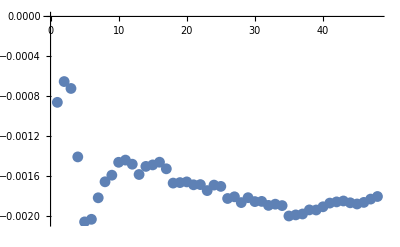

```mathematica
ListPlot[filacLog[[1]]]
```

```mathematica
filacLogFits = Table[LinearModelFit[filacLog[[i]],x,x],{i,1,Length[filacLog]}];
```

```mathematica
filacPls = Table[-1/(2*D[filacLogFits[[i]]["BestFit"],x]),{i,1,Length[filacLogFits]}];
```

```mathematica
filacPls
```

{35741.8,35741.8}

```mathematica
filacFitR2 = Table[filacLogFits[[i]]["RSquared"],{i,1,Length[filacLogFits]}];
```

```mathematica
filacFitR2
```

{0.419562,0.419562}

H_0: There is no linear trend between Log[cos(Δθ(x))] and x
A low p-value indicates that we can reject this null hypothesis

```mathematica
kl2acPVals=Table[kl2acLogFits[[i]]["ANOVATablePValues"][[1]],{i,1,Length[kl2acLogFits]}];
kl3acPVals=Table[kl3acLogFits[[i]]["ANOVATablePValues"][[1]],{i,1,Length[kl3acLogFits]}];
```

```mathematica
pvalQ[x_] := If[x<0.1,True,False];
```

```mathematica
goodKl2Pls=Pick[kl2acPls, kl2acPVals,_?pvalQ];  
goodKl3Pls=Pick[kl3acPls, kl3acPVals,_?pvalQ];
```

```mathematica
goodKl3Pls
```

{17.0307,21.6759,64.6076,24.9214,42.1363,15.6629,37.7926,-88.5111,35.6748,43.7922,57.7771,23.2302,33.2638,38.07}

```mathematica
Mean[goodKl2Pls]
```

26.3858

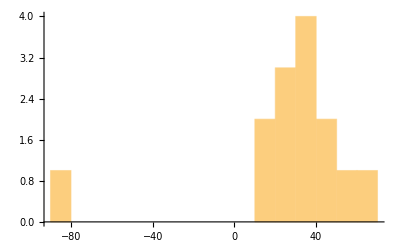

```mathematica
Histogram[goodKl3Pls,20]
```

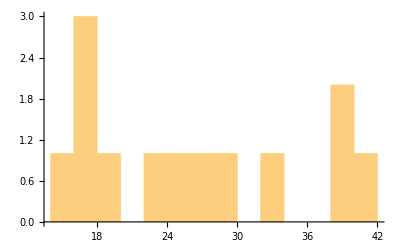

```mathematica
Histogram[goodKl2Pls,15]
```

```mathematica
StandardDeviation[goodKl2Pls]
```

9.12223

```mathematica
StandardDeviation[goodKl3Pls]
```

35.9864

```mathematica
klfm=Table[ReadList[fmPath["0.5",10,i],Number,RecordLists->True],{i,0,16}];
```

```mathematica
Manipulate[ListLinePlot[klfm[[i]]],{i,1,Length[klfm]}]
```

Part::partd: Part specification WolframAlphaClient`Private`klfm ⟦ 1. ⟧ is longer than depth of object.

Part::pkspec1: The expression False cannot be used as a part specification.

ListLinePlot::lpn: WolframAlphaClient`Private`klfm ⟦ 1. ⟧ is not a list of numbers or pairs of numbers.

Part::partd: Part specification WolframAlphaClient`Private`klfm ⟦ 1. ⟧ is longer than depth of object.

Part::pkspec1: The expression False cannot be used as a part specification.

ListLinePlot::lpn: WolframAlphaClient`Private`klfm ⟦ 1. ⟧ is not a list of numbers or pairs of numbers.